# Puntos de Lagrange

## Problema de los 3 Cuerpos Restringido

### Diego Sarceño 201900109

## Sistema Tierra - Luna

### Constantes:

```mathematica
Me =5.972*10^24
Ml = 7.349*10^22 
a = 3.844*10^8
G=6.6738*10^-11
```

5.972×10^24

7.349×10^22

3.844×10^8

6.6738×10^-11

```mathematica
ξ1 = Ml/(Ml + Me)
ξ2 = -Me/(Me + Ml)
Ktl = ((Me + Ml)*G)/a
```

0.0121562

-0.987844

1.04959×10^6

### Potencial:

```mathematica
ϕ=Ktl*(ξ2/(√((ξ - ξ1)^2+η^2))-ξ1/(√((ξ - ξ2)^2+η^2))-1/2*(ξ^2+η^2))
```

1.04959×10^6 (-0.987844/(√(η^2+(-0.0121562+ξ)^2))+1/2 (-η^2-ξ^2)-0.0121562/(√(η^2+(0.987844+ξ)^2)))

### Gráficando el potencial:

```mathematica
Plot3D[ϕ,{ξ,-2.5,2.5},{η,-1.5,1.5}]
```

-Graphics3D-

### Superficies de Nivel:

```mathematica
CPme=ContourPlot[ϕ,{ξ,-1.2,1.2},{η,-1.2,1.2},Contours-> {Automatic,200},ColorFunction->GrayLevel, GridLines->{{-1.2,-1.1,-1,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2},{-1.2,-1.1,-1,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2}},PlotLegends->Automatic]
```

-Graphics-

```mathematica
LagrangeMoonEarth={{-1.15,0},{-0.835,0},{1,0},{-0.6,0.8},{-0.6,-0.8}}
```

{{-1.15,0},{-0.835,0},{1,0},{-0.6,0.8},{-0.6,-0.8}}

```mathematica
Show[CPme,ListPlot[LagrangeMoonEarth]]
```

-Graphics-

```mathematica
NSolve[{D[ϕ,ξ]==0,D[ϕ,η]==0},{ξ,η}]
```

{{η→0,ξ→-1.1557},{η→-0.866025,ξ→-0.487844},{η→0.866025,ξ→-0.487844},{η→0.866025,ξ→-0.487844},{η→0,ξ→1.00506},{η→0,ξ→-0.836888},{η→0,ξ→-0.836888}}

```mathematica
NumLagrangeMoonEarth={{-1.1557036369372926,0},{-0.4878438306903161,-0.8660254037844392},{-0.48784383069031695,0.8660254037844386},{1.0050649722162115,0},{-0.8368876545659425,0}}
```

{{-1.1557,0},{-0.487844,-0.866025},{-0.487844,0.866025},{1.00506,0},{-0.836888,0}}

```mathematica
Show[CPme,ListPlot[NumLagrangeMoonEarth,ColorFunction->Hue]]
```

-Graphics-

## Sistema Sol - Tierra

### Constantes:

```mathematica
Ms=1.989*10^30
Me=5.972*10^24
Rse=1.5*10^11
```

1.989×10^30

5.972×10^24

1.5×10^11

```mathematica
ξ5=Me/(Ms+Me)
ξ6=-Ms/(Me+Ms)
kse=((Ms + Me)*G)/Rse
```

3.0025×10^-6

-0.999997

8.84949×10^8

### Potencial:

```mathematica
ϕ3=kse*(ξ6/(√((ξ - ξ5)^2+η^2))-ξ5/(√((ξ - ξ6)^2+η^2))-1/2*(ξ^2+η^2))
```

8.84949×10^8 (-0.999997/(√(η^2+(-3.0025×10^-6+ξ)^2))+1/2 (-η^2-ξ^2)-(3.0025×10^-6)/(√(η^2+(0.999997+ξ)^2)))

### Graficando Potencial:

```mathematica
Plot3D[ϕ3,{ξ,-2.5,2.5},{η,-2.5,2.5},ColorFunction->Hue]
```

-Graphics3D-

### Superficies de Nivel:

```mathematica
CPes=ContourPlot[ϕ3,{ξ,-1.2,1.2},{η,-1.2,1.2},Contours-> {Automatic,200},ColorFunction->GrayLevel, GridLines->Automatic,PlotLegends->Automatic]
```

-Graphics-

```mathematica
NSolve[{D[ϕ3,ξ]==0,D[ϕ3,η]},{ξ,η}]
```

{{η→0,ξ→-1.01003},{η→-0.866025,ξ→-0.499997},{η→0.866025,ξ→-0.499997},{η→0.866025,ξ→-0.499997},{η→0,ξ→1.},{η→0,ξ→-0.990028}}

```mathematica
NumLagrangeEarthSun={{-1.0100330267223583,0},{-0.49999699750476845,-0.8660254037789084},{-0.4999969975199599,0.8660254037701363},{-0.4999969975047734,0.8660254037789056},{1.0000012510436713,0},{-0.9900276710713488,0}}
```

{{-1.01003,0},{-0.499997,-0.866025},{-0.499997,0.866025},{-0.499997,0.866025},{1.,0},{-0.990028,0}}

```mathematica
Show[CPes,ListPlot[NumLagrangeEarthSun],ColorFunction-> Hue]
```

-Graphics-

## Sistema Sol - Júpiter

### Constantes:

```mathematica
Ms=1.989*10^30
Mj= 1.898*10^27
Rsj=7.50*10^11
```

1.989×10^30

1.898×10^27

7.5×10^11

```mathematica
ξ3 = Mj/(Ms + Mj)
ξ4 = -Ms/(Mj + Ms)
```

0.000953339

-0.999047

```mathematica
ksj = ((Ms + Mj)*G)/Rsj
```

1.77158×10^8

### Potencial:

```mathematica
ϕ2=ksj*(ξ4/(√((ξ - ξ3)^2+η^2))-ξ3/(√((ξ - ξ4)^2+η^2))-1/2*(ξ^2+η^2))
```

1.77158×10^8 (-0.999047/(√(η^2+(-0.000953339+ξ)^2))+1/2 (-η^2-ξ^2)-0.000953339/(√(η^2+(0.999047+ξ)^2)))

### Graficando el Potencial:

#### Potencial:

```mathematica
surfacePotential=Plot3D[ϕ2,{ξ,-2.5,2.5},{η,-1.5,1.5},ColorFunction->Hue]
```

-Graphics3D-

#### Superficies de Nivel:

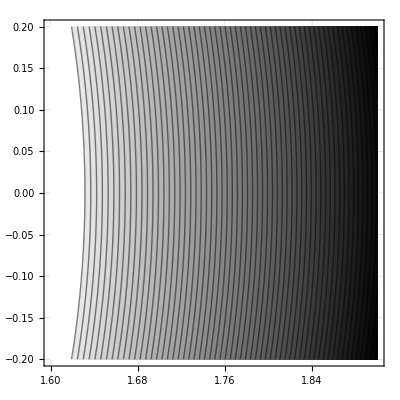

```mathematica
ContourPlot[ϕ2,{ξ,1.6,1.9},{η,-0.2,0.2},Contours-> 60,ColorFunction->GrayLevel, GridLines->Automatic]
```

```mathematica
CPjs=ContourPlot[ϕ2,{ξ,-1.2,1.2},{η,-1.2,1.2},Contours-> {Automatic,250},ColorFunction->GrayLevel, GridLines->Automatic,PlotLegends->Automatic]
```

-Graphics-

```mathematica
NSolve[{D[ϕ2,ξ]==0,D[ϕ2,η]==0},{ξ,η}]
```

{{η→0,ξ→-1.06882},{η→-0.866025,ξ→-0.499047},{η→0.866025,ξ→-0.499047},{η→0.866025,ξ→-0.499047},{η→0,ξ→1.0004},{η→0,ξ→-0.932378},{η→0,ξ→-0.932378}}

```mathematica
NumLagrangeJupiterSun={{-1.0688176812557681,0},{-0.4990466613558846,-0.8660254037844087},{-0.49904666135587494,0.8660254037844127},{-0.4990466613558684,0.866025403784429},{1.0003972243879535,0},{-0.93237833686541,0},{-0.9323783368654087,0}}
```

{{-1.06882,0},{-0.499047,-0.866025},{-0.499047,0.866025},{-0.499047,0.866025},{1.0004,0},{-0.932378,0},{-0.932378,0}}

```mathematica
Show[CPjs,ListPlot[NumLagrangeJupiterSun,ColorFunction->"Rainbow"]]
```

-Graphics-